# Chapter 6 - Problem 1

```mathematica
Clear["Global`*"];
```

So first we need our constants, along with our PP-PI matrix functions

## Part I. Declare the constants and functions we will use.

PI-PP matrix functions

```mathematica
Clear["Global`*"];
PI[kL_,kR_]= MatrixExp[(1/2) * Log[kL/kR] * ( PauliMatrix[1] - IdentityMatrix[2])];
PP [kx_,l_] = MatrixExp[-I * kx * l * PauliMatrix[3]];
```

Constants (we’ll always use these numbers)

```mathematica
h = 6.62607004 * 10^(-34) ;(* planck's constant *)
m = 9.10938 * 10^(-31); (* planck's constant *)
ℏ = h/(2*Pi);
```

Conversion factors:

```mathematica
e = 1.60217 * 10 ^(-19); (* 1 electron volt (ev) = e Joules *)
nano = 1 *10^(-9);
```

Given information and other constants/functions:

```mathematica
λ = 0.3;
L = 0.4;
alpha = √((2*m*e)/ℏ^2) * nano; (* the e and nano will help convert everything at once.*)
k = alpha * √epi;
kdelta = alpha * √(epi-λ/a);
numofbarriers = 1; (* This is artbitrary as long as we keep this constant throughout all the subsequent problems *)
```

## Part II. Get the Transfer Matrix

The transfer matrix in this case is made up of PP.PI.PP.and one more PI. Raised to the matrix power of 3 (because we chose 3 to be our number of barriers). You can see above that we set this to a variable that can be changed if we decide that 3 is too many (or too
 few).

```mathematica
TransferMatrix = PI[k,kdelta].PP[kdelta,a].PI[kdelta,k].PP[k,L];
```

Now we can use MatrixPower, and since we are using delta approximation then we have to take the Limit as 
“a” approaches 0. Because a delta function has a width of 0. Then plot.

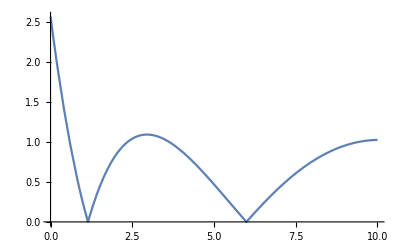

```mathematica
TransferMatrix= Limit[MatrixPower[TransferMatrix,numofbarriers](*.PP[k,L]*),a->0];
TransferPlot = Plot[Abs[Tr[TransferMatrix]/(2)],{epi,0,10}]
```

## Part III. Finding the Forbidden Zone

Okay so to find the find the forbidden bands,  we need this:
1. Plot |1/2 Tr[TransferMatrix]|with respect to energy -> we just did this
2. Let's call this P[[1,1]] -> this is what he calls it in this notes
3. Then on Chapter 5 Page 6, this value must satisfy the following equation to be allowed. |P_11| <= 1
4. In other words, the forbidden zone is located when this condition is NOT satisfied. That is...the energy is forbidden if: |P_11| > 1.
Okay so let's get these forbidden bands...

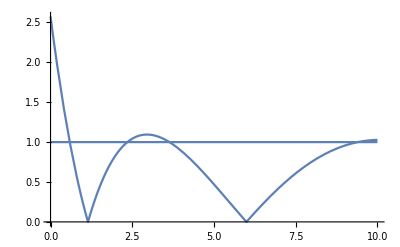

```mathematica
lineatone = Plot[1,{epi,0,10}];
Show[TransferPlot,lineatone]
```

Okay so we can clearly see the the forbidden bands now. We can use FindRoot to find this because you can find when f(x) == 1 using FindRoot as well. Let’s try it along with the for loop method that we tried in problem 5.7.

```mathematica
(* Try to find one root *)
```

```mathematica
Subscript[P, 11]= Tr[TransferMatrix/2];
FindRoot[Abs[Subscript[P, 11]]== 1,{epi,2.2}]
```

{epi→2.3502}

```mathematica
(* Okay our test worked, so let's use the for loop method *)
NumOfRoots = 2;
Array[ForbiddenRoots, NumOfRoots ]; (* Results *)
Array[StartSearch,NumOfRoots ,1]; (* where to search *)
StartSearch[1] = 2.2; 
StartSearch[2] = 2.5;
 For[i = 1 , i <= NumOfRoots , i++,
ForbiddenRoots[i]= epi/.FindRoot[Abs[Subscript[P, 11]]==1,{epi,StartSearch[i]}];]
For[i = 1, i <=NumOfRoots , i+= 2,
Print["Forbidden band from \n\t", ForbiddenRoots[i], " eV to ", ForbiddenRoots[i+1], " eV"]]
```

Forbidden band from 
	2.3502 eV to 2.3502 eV

Note: If you increase the number of barriers you use, this forbidden band will not change

The first and last roots aren’t within the bounds of 0 - 10 eV, thus we won’t look at them. Within the given the range, there are 3 forbidden bands listed above.
Below is Chapter 6 page 5, which shows what the condition needs to be to be considered a forbidden band.

-Graphics-
Kelvin